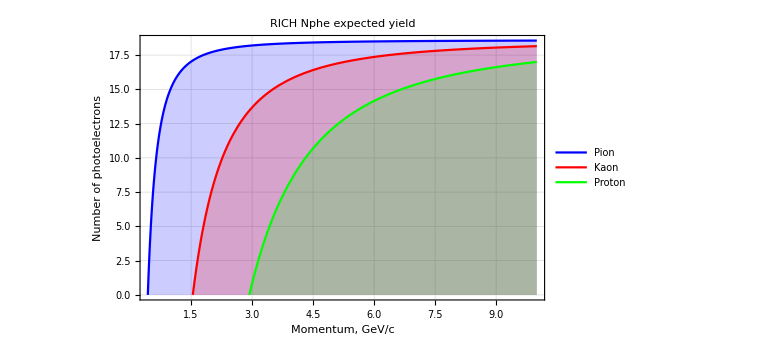

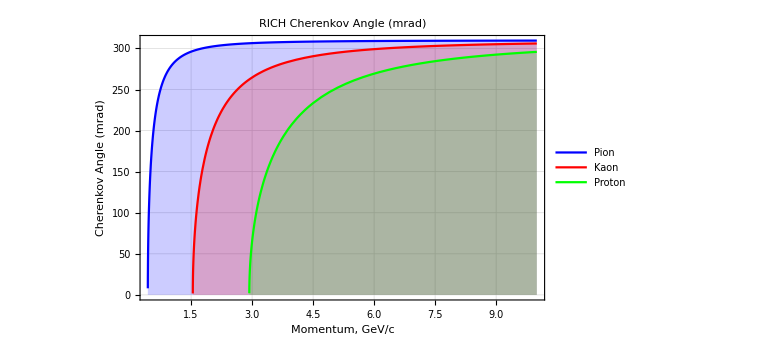

-Graphics-

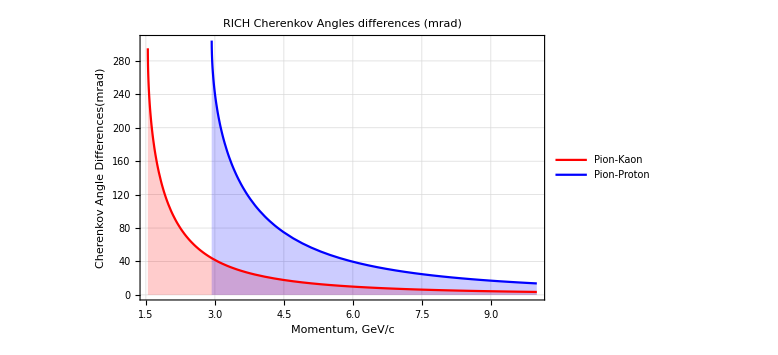

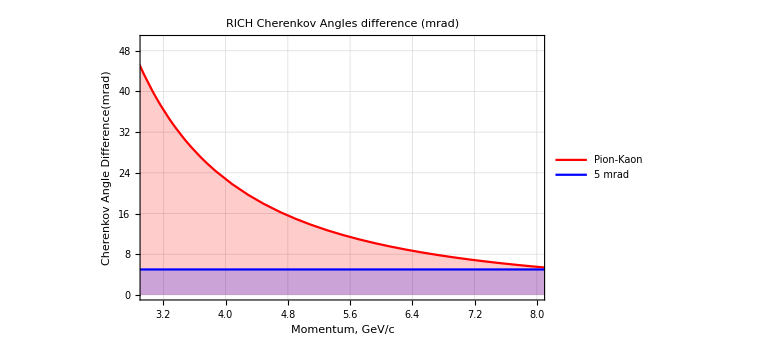

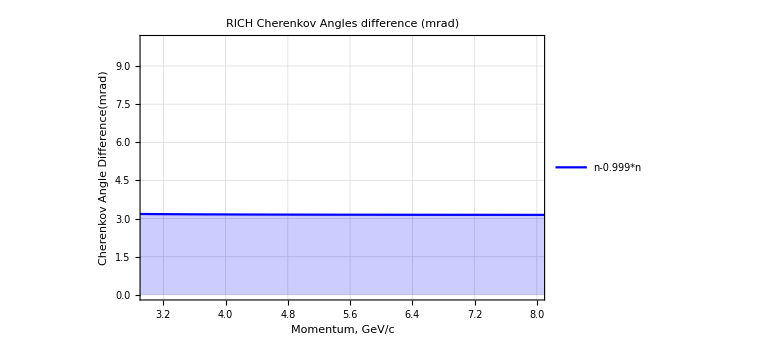

```mathematica
ChAngle[m_,p_,n_]:=ArcCos[1./n/(p/Sqrt[p^2+m^2])];
Chmrad[m_,p_,n_]:=1000*ArcCos[1./n/(p/Sqrt[p^2+m^2])];
Nphe[m_,p_,n_,l_,fofm_]:=l*fom*Sin[changle[m,p,n]]^2;

nco2=1.00044892;
nneon=1.000066102;
naero=1.05;
l=2;
fom=100;
n=naero;
pmax=10;

Plot[{Nphe[mpi,p,n,l,fom],Nphe[mk,p,n,l,fom],Nphe[mp,p,n,l,fom]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Number of photoelectrons"},
PlotLabel->"RICH Nphe expected yield",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
Filling->Axis,
PlotStyle->{Blue,Red,Green},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]

Plot[{Chmrad[mpi,p,n],Chmrad[mk,p,n],Chmrad[mp,p,n]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle (mrad)"},
PlotLabel->"RICH Cherenkov Angle (mrad)",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
Filling->Axis,
PlotStyle->{Blue,Red,Green},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]

Plot[{Nphe[mpi,p,n,l,fom],Nphe[mk,p,n,l,fom],Nphe[mp,p,n,l,fom]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Number of photoelectrons"},
PlotLabel->"RICH Nphe expected yield",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
Filling->Axis,
PlotStyle->{Blue,Red,Green},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]

Plot[{Chmrad[mpi,p,n]-Chmrad[mk,p,n],Chmrad[mpi,p,n]-Chmrad[mp,p,n]},{p,0,pmax},PlotRange->{{3,8},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Differences(mrad)"},
PlotLabel->"RICH Cherenkov Angles differences (mrad)",
PlotLegends->Placed[{"Pion-Kaon","Pion-Proton"},Center],
Filling->Axis,
PlotStyle->{Red,Blue,Green},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]

Plot[{Chmrad[mpi,p,n]-Chmrad[mk,p,n],5},{p,0,pmax},PlotRange->{{3,8},{0,50}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Difference(mrad)"},
PlotLabel->"RICH Cherenkov Angles difference (mrad)",
PlotLegends->Placed[{"Pion-Kaon","5 mrad"},Center],
Filling->Axis,
PlotStyle->{Red,Blue},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]

Plot[{Chmrad[mpi,p,n]-Chmrad[mpi,p,n*0.999]},{p,0,pmax},PlotRange->{{3,8},{0,10}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Difference(mrad)"},
PlotLabel->"RICH Cherenkov Angles difference (mrad)",
PlotLegends->Placed[{"n-0.999*n"},Center],
Filling->Axis,
PlotStyle->{Red,Blue},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic]
```

```mathematica
ll=100; R=ll*Tan[0.3];
a1=ArcTan[R/ll]
a2=ArcTan[R/(ll+0.5)]
a1-a2
a3=ArcTan[(R+0.5)/ll]
a3-a1
2/Sqrt[12.]
```

0.3

0.298595

0.00140519

0.304557

0.00455687

0.57735

```mathematica
30.93362496096232
```